```mathematica
CollectMPGEdges[SortGraph[ReadGrof[11]]]
```

{1<->2,1<->3,1<->7,2<->5,2<->6,3<->4,3<->6,3<->8,4<->5,4<->6,4<->8,5<->6,5<->7,5<->8,7<->8}

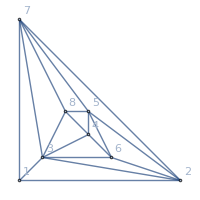
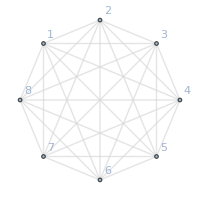
-Graphics-<->-Graphics-{10,{v18x24x35x67,v14x28x35x67,v168x2x35x47,v16x28x35x47,v168x24x35x7}}

```mathematica
With[{g=ReadGrof[11]},Labeled[Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding",ImageSize->200,GraphHighlight->{UndirectedEdge[1,7]},EdgeStyle->Map[#->{Thick,Blue}&,CollectMPGEdges[g]],GraphHighlightStyle->"Thick"]<->Graph[BeautiGraph[g],ImageSize->200],{EdgeCount[GraphComplement[g]],FindFullFormula4[g]}]]
```

```mathematica
v14x2x5x68
```

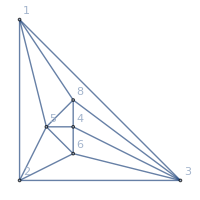
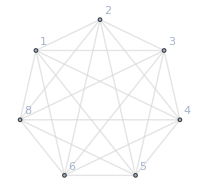
-Graphics-<->-Graphics-{6,{v14x2x35x68,v14x28x35x6,v16x28x35x4,v16x24x35x8,v1x24x35x68}}

```mathematica
With[{g=VertexContract[ReadGrof[11],{1,7}]},Labeled[Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding",ImageSize->200,GraphHighlight->{UndirectedEdge[2,3]},GraphHighlightStyle->"Thick",EdgeStyle->Map[#->{Thick,Blue}&,CollectMPGEdges[g]]]<->Graph[BeautiGraph[g],ImageSize->200],{EdgeCount[GraphComplement[g]],FindFullFormula4[g]}]]
```

```mathematica
v14x2x5x8
```

```mathematica
With[{g=VertexContract[ReadGrof[11],{1,7}]},CollectMPGEdges[g]]
```

{2<->3,2<->5,2<->6,3<->4,3<->6,3<->8,4<->5,4<->6,4<->8,5<->6,5<->8,1<->2,1<->3,1<->5,1<->8}

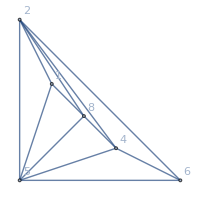
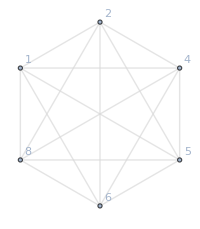
-Graphics-<->-Graphics-{3,{v14x2x5x68}}

```mathematica
With[{h=VertexContract[ReadGrof[11],{1,7}]},With[{g=VertexContract[h,{2,3}]},Labeled[Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding",ImageSize->200,GraphHighlight->{UndirectedEdge[4,6]},GraphHighlightStyle->"Thick",EdgeStyle->Map[#->{Thick,Blue}&,CollectMPGEdges[g]]]<->Graph[BeautiGraph[g],ImageSize->200],{EdgeCount[GraphComplement[g]],FindFullFormula4[g]}]]]
```

```mathematica
With[{h=VertexContract[ReadGrof[11],{1,7}]},With[{g=VertexContract[h,{2,3}]},CollectMPGEdges[g]]]
```

{4<->6,4<->8,5<->6,1<->5,1<->8,2<->1,2<->6}

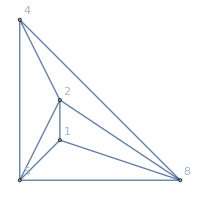
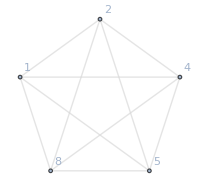
-Graphics-<->-Graphics-{1,{v14x2x5x8}}

```mathematica
With[{i=VertexContract[ReadGrof[11],{1,7}]},With[{h=VertexContract[i,{2,3}]},With[{g=VertexContract[h,{4,6}]},Labeled[Graph[g,VertexLabels->"Name",GraphLayout->"PlanarEmbedding",ImageSize->200,EdgeStyle->Map[#->{Thick,Blue}&,CollectMPGEdges[g]]]<->Graph[BeautiGraph[g],ImageSize->200],{EdgeCount[GraphComplement[g]],FindFullFormula4[g]}]]]]
```

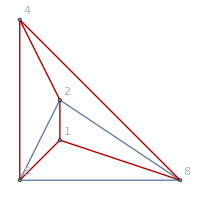

```mathematica
With[{g=-Graphics-},Graph[g,GraphHighlight->CollectMPGEdges[g]]]
```